```mathematica
h[x_]:=Piecewise[{{1+c01 x+c02 x^2, 0≤x≤1}, {c11(x-1)+c12(x-1)^2, 1<x≤2}, {0, True}}];
f[x_]:=h[Abs[x]];
```

```mathematica
(*Interpolant constraints*)
I1=f[1]
I2=f[2]
```

1+c01+c02

c11+c12

```mathematica
(*Partition of unity and gradient representation*)
T0=CoefficientList[FullSimplify[f[x+1]+f[x]+f[x-1]+f[x-2],x>0&&x<1],x]
T1=CoefficientList[FullSimplify[-f[x+1]+f[x-1]+2f[x-2],x>0&&x<1],x]
```

{2+c01+c02+c11+c12,-2 (c02+c12),2 (c02+c12)}

{1+c01+c02+2 c11+2 c12,-c01-2 c02-3 c11-4 c12,c02+c12}

```mathematica
GenSols=Solve[{
	I1==0,
	I2==0,
	T0[[1]]==1,
	T0[[2]]==0,
	T0[[3]]==0,
	T1[[1]]==0,
	T1[[2]]==1,
	T1[[3]]==0
	},
	{c01,c02,c11,c12}
]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{c02→-1-c01,c11→-1-c01,c12→1+c01}}

```mathematica
GenSol=GenSols[[1]];
f[x_,y_]:=f[x]f[y];
W1[k_]:=Piecewise[{{0, k<0}, {φ^2/2, k==0}, {1-(1-φ)^2/2, k==1}, {1, True}}];
SumF1=∑_(i=-3)^5 ∑_(j=-3)^5 W1[i-j]f[x-i,y-j]/.GenSol;
{SumF1a1,SumF1a2,SumF1a3,SumF1a4}=Parallelize[{
	Simplify[SumF1,x>0&&x<1&&y>0&&y<1],
	Simplify[SumF1,x>0&&x<1&&y>1&&y<2],
	Simplify[SumF1,x>-1&&x<0&&y>1&&y<2],
	Simplify[SumF1,x>-1&&x<0&&y>2&&y<3]}];
{DSumF1a1,DSumF1a2,DSumF1a3,DSumF1a4}=Parallelize[{
	FullSimplify[D[SumF1a1,{{x,y}}]],
	FullSimplify[D[SumF1a2,{{x,y}}]],
	FullSimplify[D[SumF1a3,{{x,y}}]],
	FullSimplify[D[SumF1a4,{{x,y}}]]}];
{SumF1b1,SumF1b2,SumF1b3,SumF1b4}=Parallelize[{
	Simplify[SumF1,x>1&&x<2&&y>0&&y<1],
	Simplify[SumF1,x>1&&x<2&&y>-1&&y<0],
	Simplify[SumF1,x>2&&x<3&&y>-1&&y<0],
	Simplify[SumF1,x>2&&x<3&&y>-2&&y<-1]}];
{DSumF1b1,DSumF1b2,DSumF1b3,DSumF1b4}=Parallelize[{
	FullSimplify[D[SumF1b1,{{x,y}}]],
	FullSimplify[D[SumF1b2,{{x,y}}]],
	FullSimplify[D[SumF1b3,{{x,y}}]],
	FullSimplify[D[SumF1b4,{{x,y}}]]}];
```

```mathematica
{Err1a1,Err1a2,Err1a3,Err1a4}=Parallelize[{
	Simplify[∫_0^1 ∫_0^1 (DSumF1a1.{1,1})^2 ⅆxⅆy],
	Simplify[∫_1^2 ∫_0^1 (DSumF1a2.{1,1})^2 ⅆxⅆy],
	Simplify[∫_1^2 ∫_-1^0 (DSumF1a3.{1,1})^2 ⅆxⅆy],
	Simplify[∫_2^3 ∫_-1^0 (DSumF1a4.{1,1})^2 ⅆxⅆy]}];
```

```mathematica
{Err1b1,Err1b2,Err1b3,Err1b4}=Parallelize[{
	Simplify[∫_0^1 ∫_1^2 (DSumF1b1.{1,1})^2 ⅆxⅆy],
	Simplify[∫_-1^0 ∫_1^2 (DSumF1b2.{1,1})^2 ⅆxⅆy],
	Simplify[∫_-1^0 ∫_2^3 (DSumF1b3.{1,1})^2 ⅆxⅆy],
	Simplify[∫_-2^-1 ∫_2^3 (DSumF1b4.{1,1})^2 ⅆxⅆy]}];
```

```mathematica
Err1=FullSimplify[Err1a1+Err1a2+Err1a3+Err1a4+Err1b1+Err1b2+Err1b3+Err1b4];
```

```mathematica
Err=FullSimplify[Err1/.φ->1/2]
DErr=FullSimplify[D[Err,c01]];
H=D[DErr,c01];
Sols=RootReduce[Solve[DErr==0,c01]];
N[Sols]
RootReduce[Sols[[1]]]
TableForm[{Range[Length[Sols]],Err/.N[Sols],Sign[H/.N[Sols]]}ᵀ]
```

(752+c01 (2611+2 c01 (1596+c01 (667+98 c01))))/1440

{{c01→-0.621913},{c01→-2.24134+0.57569 ⅈ},{c01→-2.24134-0.57569 ⅈ}}

{c01→Root[2611+6384 #1+4002 #1^2+784 #1^3&,1]}

1 | 0.0494532 | 1
2 | 0.583152-0.112147 ⅈ | -0.334955-0.942234 ⅈ
3 | 0.583152+0.112147 ⅈ | -0.334955+0.942234 ⅈ

{c02→-0.378087,c11→-0.378087,c12→0.378087,c01→-0.621913}

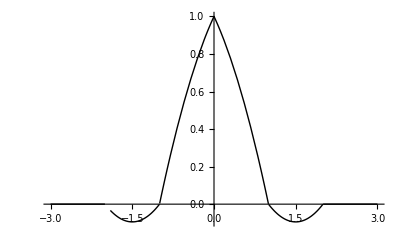

```mathematica
Sol=Sols[[1]];
FullSol=N[Join[GenSol/.Sol,Sol]]
fo[x_]:=f[x]/.FullSol;
Plot[fo[x],{x,-3,3},PlotStyle->Black,Background->White]
```